Caderno de Física Matemática I

## - Aula 02: Coeficientes de Fourier

Usamos as funções FourierSinCoefficient[função, x, n] e FourierCosCoefficient[função, x, n] para calcular os coeficientes de fourier, devemos prestar atenção que o Mathematica calcula esses coeficientes com os limites da integral indo de [0, π].

0

-(2 (-1+(-1)^n) função)/(n π)

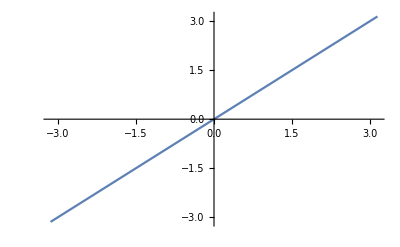

```mathematica
FourierCosCoefficient[função, x , n]
FourierSinCoefficient[função, x, n]
Plot[x,{x,-π,π}]
```

Observamos durante as aulas que:

```mathematica
Subscript[a, n]= 0 ; Subscript[b, n]≠ 0
```

```mathematica
FourierSinCoefficient[x,x,n]
```

-(2 (-1)^n)/n

```mathematica
FourierCosCoefficient[x,x,n]
```

(2 (-1+(-1)^n))/(n^2 π)

O resultado acima está errado, o coeficiente foi integrado no período [0,π], sendo que o correto seria [-π,π]. No período certo o resultado seria zero.

```mathematica
1/π*Integrate[x*Cos[n x], {x,-π,π}, Assumptions->n ∈ Integers]
```

0

```mathematica
1/π*Integrate[x*Sin[n x], {x,-π,π}, Assumptions->n ∈ Integers]
```

(2 (-n π Cos[n π]+Sin[n π]))/(n^2 π)

```mathematica
FullSimplify[%, n ∈ Integers]
```

-(2 (-1)^n)/n

Seja f[x] uma função qualquer. Para deixa-la periódica por partes, com período L, use f[Mod[x,L,-L/2]]. A função Mod calcula x módulo L. O terceiro argumento é o offset, quando ele é -L/2, estamos pegando a função entre [-L/2, L/2]. Se o terceiro argumento fosse 0 então repetiríamos a função dentro do intervalo [0, L]. 
Abaixo veremos os exemplos estudados em aula:

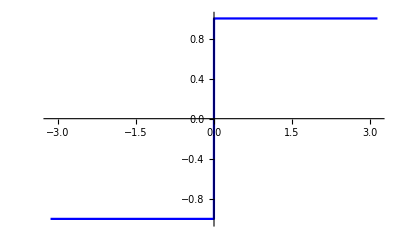

```mathematica
Plot[Sign[x],{x,-π,π},Exclusions->None,PlotRange->{-1.03,1.02},PlotStyle->Blue]
```

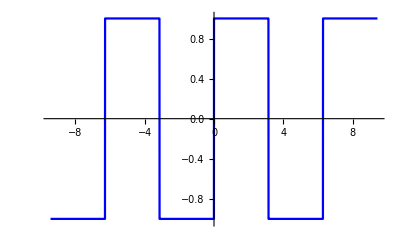

```mathematica
Plot[Sign[Mod[x,2π,-π]],{x,-3π,3π},Exclusions->None,PlotRange->{-1.03,1.02},PlotStyle->Blue]
```

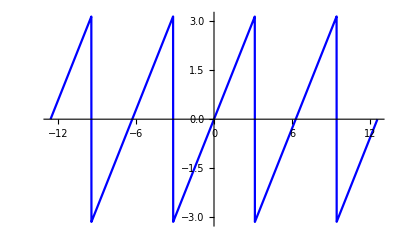

```mathematica
Plot[Mod[x,2π,-π],{x,-4π,4π},PlotStyle->Blue,Exclusions->None]
```

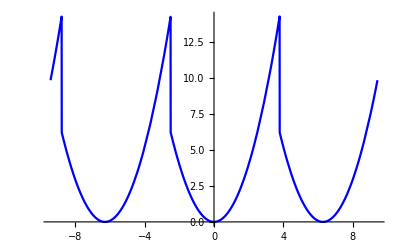

```mathematica
Plot[Mod[x,2π,-2.5]^2,{x,-3π,3π},PlotStyle->Blue]
```

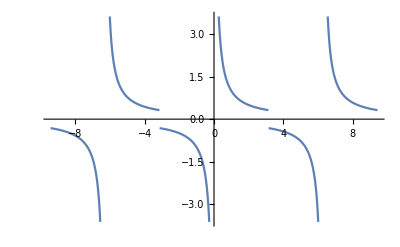

```mathematica
meuplot=Plot[1/Mod[x,2π,-π],{x,-3π,3π}]
```

```mathematica
(* Para salvar um gráfico;
ou clique no gráfico e vá em "Save Selection As"*)
```

```mathematica
Export["filepath.pdf", meuplot]
```

filepath.pdf

```mathematica
FourierSinCoefficient[Sign[x],x,n]
```

-(2 (-1+(-1)^n))/(n π)

```mathematica
(* n indo de 1 até 20 em passos de 2 *)
Sum[4/(n π)Sin[n x] ,{n,1,20,2}]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)+(4 Sin[11 x])/(11 π)+(4 Sin[13 x])/(13 π)+(4 Sin[15 x])/(15 π)+(4 Sin[17 x])/(17 π)+(4 Sin[19 x])/(19 π)

```mathematica
Sum[4/(n π)Sin[n x],{n,1,20,2}]
Sum [(1/(n π)) [Sin[n *v]-Sin[u* n]]*Cos[n* x],{n, 1,4}]- Sum [(1/(n π)) [Cos[n* v]-Cos[u* n]]*Sin[n *x],{n, 1,4}]
```

(4 Sin[x])/π+(4 Sin[3 x])/(3 π)+(4 Sin[5 x])/(5 π)+(4 Sin[7 x])/(7 π)+(4 Sin[9 x])/(9 π)+(4 Sin[11 x])/(11 π)+(4 Sin[13 x])/(13 π)+(4 Sin[15 x])/(15 π)+(4 Sin[17 x])/(17 π)+(4 Sin[19 x])/(19 π)

Cos[4 x] 1/(4 π)[2 Sin[4]]+Cos[3 x] 1/(3 π)[2 Sin[3]]+Cos[2 x] 1/(2 π)[2 Sin[2]]+Cos[x] 1/π[2 Sin[1]]-1/π[0] Sin[x]-1/(2 π)[0] Sin[2 x]-1/(3 π)[0] Sin[3 x]-1/(4 π)[0] Sin[4 x]

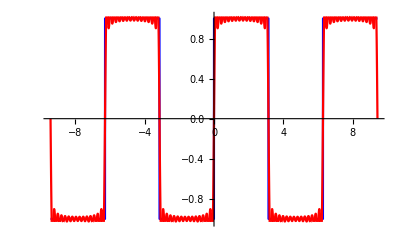

```mathematica
Plot[{
Sign[Mod[x,2π,-π]],
Sum[4/(n π)Sin[n x],{n,1,30,2}]
},{x,-3π,3π},Exclusions->None,PlotRange->{-1.03,1.02},PlotStyle->{Blue,Red}]
```

```mathematica
?Mod
```

```mathematica
- Aula 02: Exemplos de Serie de Fourier
```

Alguns exemplos de funções definidas por partes:

```mathematica
f=Piecewise[{
{x,0<x<1},
{x^3,1<x<2}
}]
```

Piecewise[{{x, 0<x<1}, {x^3, 1<x<2}, {0, True}}]

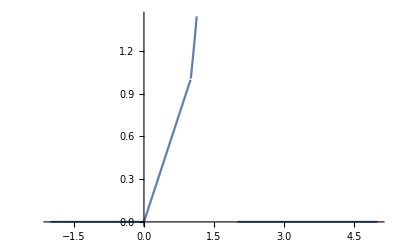

```mathematica
Plot[f,{x,-2,5}]
```

```mathematica
Clear[f];
```

```mathematica
f[x_]:=Piecewise[{
{x,0<x<1},
{x^3,1<x<2}
}]
```

Mod[x,L]:      x periódica entre [0,L]
Mod[x,L,d]:  x periódica [-d,L-d]

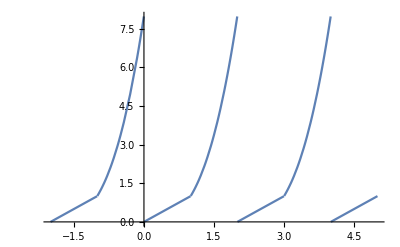

```mathematica
Plot[f[Mod[x,2]],{x,-2,5}]
```

```mathematica
Clear[f];
f[x_]:=Piecewise[{
{Tanh[x],-1/2<x<1/2},
{Cos[x],1/2<x<1}
}]
```

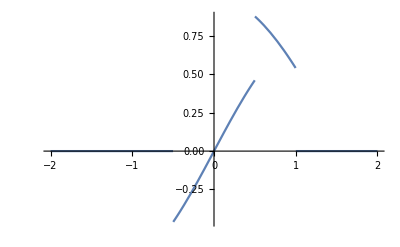

```mathematica
Plot[f[x],{x,-2,2}]
```

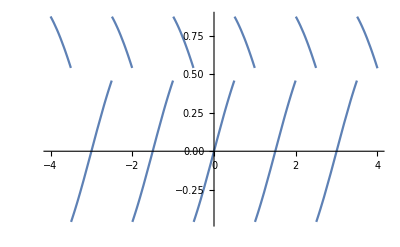

```mathematica
Plot[f[Mod[x,3/2,-1/2]],{x,-4,4}]
```

Customização de gráficos

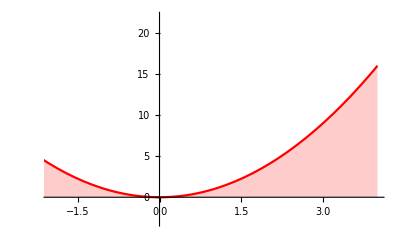

```mathematica
Plot[x^2,{x,-4,4},
PlotRange->{{-2,4},{-3,22}},
PlotStyle->Red,
Filling->Axis
]
```

## - Aula 07: Fourier and Sound

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[Plot,ImagePadding->{{60,20},{40,10}},ExclusionsStyle->Dashed,AspectRatio->1/3,ImageSize->750,PlotStyle->Blue, Frame->True];
```

# Application of Fourier series to sound

Sound propagates as pressure waves in air. 
When this wave reaches our ears, it causes tiny bones in the inner ear to wiggle. 
These, in turn, agitate a fluid which is then detected by hair cells that convert this movement into electrical pulses. 

Hearing is therefore associated with pressure waves. 
Let p(t) describe the variations of the pressure, around the ambient value,  that arrive in our ears. 
- The tone of the sound will be associated to the frequency of p(t). 
- The intensity of the sound will be associated with the absolute value |p(t)|^2

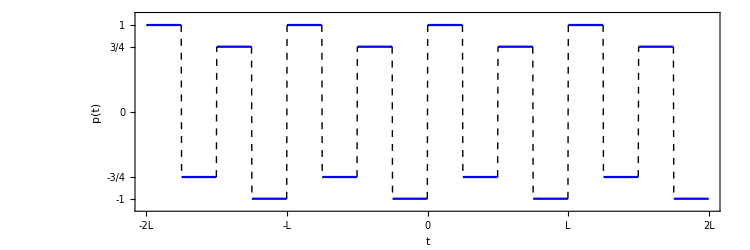

```mathematica
Clear[f,L,ν];
ν = 524; (* Subscript[C, 5] *)
L = 1/ν;
h =3/4;
f[x_]:=Piecewise[{
{1,0<x<L/4},
{-h,L/4<x<(2L)/4},
{h,(2L)/4<x<(3L)/4},
{-1,(3L)/4<x<L}}]
Plot[f[Mod[x,L]],{x,-2L,2L},PlotRange->{-1.1,1.1},
FrameTicks->{{{-1,{-h,"-3/4"},0,{h,"3/4"},{1,"1  "}},Automatic},{N@{{-2L,"-2L"},{-L,"-L"},{0,"0"},{L,"L"},{2L,"2L"}},Automatic}},
FrameLabel->{Style["t",Italic],Style["p(t)",Italic]}
]
```

Here is a psychedelic sound:

```mathematica
Play[Sin[300t Sin[20t]],{t,0,4}]
```

-Graphics-

Pure musical notes correspond to well defined sinusoidal functions

Note A in the middle of the piano, for instance, is A_4 = 440 Hz

```mathematica
Play[Sin[440 2π t],{t,0,2}]
```

-Graphics-

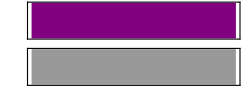

```mathematica
Sound[SoundNote["A",2,"Piano"]]
```

When talking about sound, we generally use frequency ν. 
The period L appearing in our Fourier analysis is simply

L = 1/ν

so the Fourier series becomes

f(t) = a_0/2+∑_(n = 1)^∞ [a_n cos(2π n ν t) + b_n sin(2π n ν t)]

### Combining different harmonics

Here I am using a pure sine series (only b_n≠0), with different combinations of Fourier coefficients.

(shift+enter on the code below to run; the “Manipulate” function is very heavy, so it is good practice to delete the output whenever you are not using it).

```mathematica
ν0 = 440;
Manipulate[
Play[b1 Sin[2π ν0 t] + b2 Sin[2 (2π ν0 t)] +  b3 Sin[3 (2π ν0 t)] +  b4 Sin[4 (2π ν0 t)] +  b5 Sin[5 (2π ν0 t)],{t,0,2}],
{{b1,1,"b_1"},0,5,1},{{b2,0,"b_2"},0,5,1},{{b3,0,"b_3"},0,5,1},{{b4,0,"b_4"},0,5,1},{{b5,0,"b_5"},0,5,1},ControlType->Setter,LabelStyle->Directive[22,FontFamily->"Times"]]
```

### Relative contributions from different harmonics

A sound of frequency ν, will in general contain contributions from different harmonics.
Here is an example of a sound at frequency C_5:

```mathematica
Clear[f,L,ν];
ν = 524; (* Subscript[C, 5] *)
L = 1/ν;
h =3/4;
f[x_]:=Piecewise[{
{1,0<x<L/4},
{-h,L/4<x<(2L)/4},
{h,(2L)/4<x<(3L)/4},
{-1,(3L)/4<x<L}}]
Plot[f[Mod[x,L]],{x,-2L,2L},PlotRange->{-1.1,1.1},
FrameTicks->{{{-1,{-h,"-3/4"},0,{h,"3/4"},{1,"1  "}},Automatic},{N@{{-2L,"-2L"},{-L,"-L"},{0,"0"},{L,"L"},{2L,"2L"}},Automatic}},
FrameLabel->{Style["t",Italic],Style["p(t)",Italic]}
]
```

-Graphics-

This is not a pure sinusoidal function, however. 
It will contain contributions from multiple harmonics.

This is what Fourier series is all about.

Since the pulse is odd, this can be decomposed as a sine series:

p(t) = ∑_(n = 1)^∞ b_n sin(2π n ν t)

The Fourier coefficients are

```mathematica
coefs=Table[2/L Integrate[f[x]Sin[(2π n x)/L],{x,0,L}],{n,1,10}]
```

{1/(2 π),7/(2 π),1/(6 π),0,1/(10 π),7/(6 π),1/(14 π),0,1/(18 π),7/(10 π)}

These factors of π make them a bit ugly. 
But their absolute value in this case does not matter, since that is related to the overall intensity of the sound. 
All that matters are their relative intensities: |b_n|^2/|b_1|^2

```mathematica
coefs^2/First[coefs]^2
```

{1,49,1/9,0,1/25,49/9,1/49,0,1/81,49/25}

Média do pulso sonoro ao longo de um período: identidade de Parseval,

1/L∫_0^L |p(t)|^2 dt= ∑_(n = 1)^∞ |b_n|^2

We see that even though the sound has frequency ν, the 2nd harmonic is actually much more important. 
It’s contribution is 49 times higher than the principal harmonic! 
Other harmonics contribute significantly as well, like the 6th harmonic.

```mathematica
Play[f[Mod[x,L]],{x,0,1}]
```

-Graphics-

```mathematica
(* shift+enter to run this Manipulate *)
Manipulate[Play[Sin[n 2π ν t],{t,0,1}],
{{n,1},1,10,1},ControlType->Setter,LabelStyle->Directive[20,FontFamily->"Times"]]
```

### Playing with sounds

Here I define a generalization of the step function used above, so that we can play with the relative Fourier coefficients.

```mathematica
Clear[f,L,ν,h];
f[x_,L_,h_]:=Piecewise[{
{1,0≤x<L/4},
{-h,L/4<x<(2L)/4},
{h,(2L)/4<x<(3L)/4},
{-1,(3L)/4<x≤ L}}];
```

```mathematica
bn[n_,ν_,h_]:=(4 (-1+h-2 Cos[(n π)/2]) Cos[n π] Sin[(n π)/4]^2)/(n π);

lim = 2/525;
Manipulate[
L = 1/ν;
coefs=Table[bn[n,ν,h],{n,1,10}];
tab = N[coefs^2/First[coefs]^2,3];
ttab = TableForm[Table[Style[TraditionalForm[t],FractionBoxOptions->{Beveled->True}],{t,tab}],TableHeadings->{Table[Subscript[b, i],{i,1,10}],None},TableSpacing->{3,10}];

Grid[{{Plot[f[Mod[x,L],L,h],{x,-lim,lim},PlotRange->{-1.1,1.1},
FrameTicks->{{{-1,-h,0,h,{1,"1  "}},Automatic},{N@{{-2L,"-2L"},{-L,"-L"},{0,"0"},{L,"L"},{2L,"2L"}},Automatic}},
FrameLabel->{Style["t",Italic],Style["p(t)",Italic]}
],ttab
}}]

,{{ν,525},200,800,1},{{h,3/4},0,1,1/100}]
```

Just so you know, I computed the coefficients b_n above using the following code:

```mathematica
2/L Integrate[f[x,L,h]Sin[(2π n x)/L],{x,0,L},Assumptions->L>0]/.L->1/ν//Simplify
```

(4 (-1+h-2 Cos[(n π)/2]) Cos[n π] Sin[(n π)/4]^2)/(n π)

### Template for making pretty density plots

This notebook contains a basic snippet of code for plotting pretty ContourPlots using Mathematica. 
You can use this to check the behavior of the solution of PDEs. 

I illustrate the code with the example done in the notes, corresponding to the 1D heat equation with (L = 1)

u_0(x) = x (x^2-3x +2)

The general solution is

u(x,t) = ∑_(n =1)^∞  b_n e^(-i α k_n^2 t)sin(k_n x)

where

b_n  = 2/L∫_0^L u_0(x) sin(k_n x) dx

For our example we get (L = 1)

```mathematica
bn = FullSimplify[2 Integrate[x (x^2-3x + 2) Sin[n π x],{x,0,1}],n∈Integers]
```

12/(n^3 π^3)

We now use this to define our solution. We take the sum up to a certain large value nmax.
We then plot the result. Everything else are just cosmetic options for the DensityPlot function, which you can play with if you want (α = 1):

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

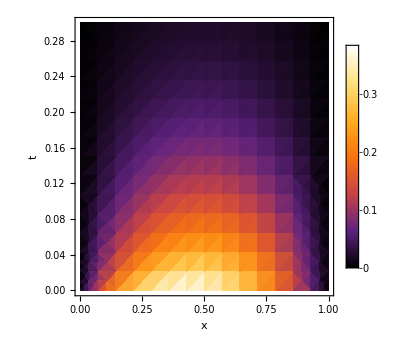

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.3},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

You can also export them as follows

```mathematica
(* Makes the default directory the same as the notebook you are working *)
SetDirectory[NotebookDirectory[]] 

(* Here "plot" is the name I gave to the plot above. *)
Export["MyFig.png",plot,ImageResolution->300];
```

I also recommend that, in the case of Density Plots, you use png instead of PDF. 
PDFs tend to get very heavy.

### Outros exemplos de condições iniciais sugeridos em aula

#### Exemplo do Marcio

```mathematica
bn=FullSimplify[2 Integrate[HeavisideTheta[x-0.4] HeavisideTheta[0.6-x]  Sin[n π x],{x,0,1}],n∈Integers]
```

(0.63662 Cos[1.25664 n]-0.63662 Cos[1.88496 n])/n

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

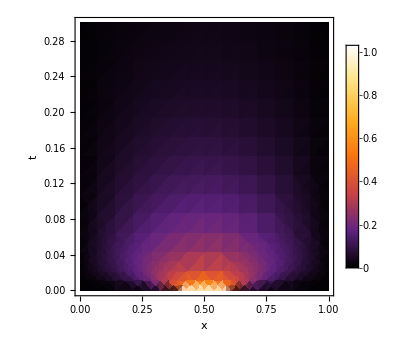

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.3},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

#### Exemplo do Thiago

```mathematica
bn=FullSimplify[2 Integrate[(Sin[10x]+1)  Sin[n π x],{x,0,1}],n∈Integers]
```

2 ((1+(-1)^(1+n))/(n π)+((-1)^(1+n) n π Sin[10])/(-100+n^2 π^2))

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

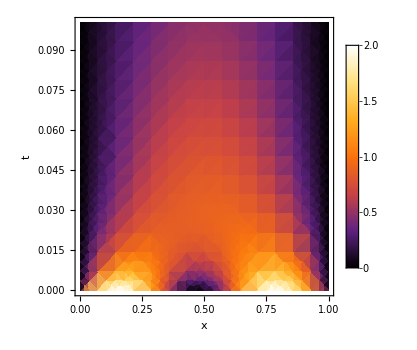

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

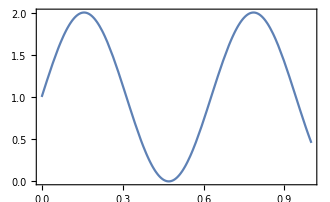

```mathematica
Plot[Sin[10x]+1,{x,0,1}]
```

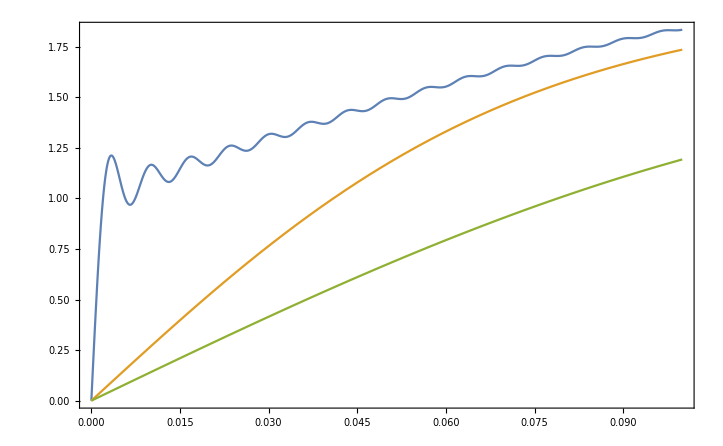

```mathematica
Quiet@Plot[Evaluate@Table[sol,{t,{0,0.001,0.005}}],{x,0,0.1}]
```

#### Exemplo do Luca

```mathematica
bn=FullSimplify[2 Integrate[Exp[-x]  Sin[n π x],{x,0,1}],n∈Integers]
```

(2 ((-1)^(1+n)+ⅇ) n π)/(ⅇ+ⅇ n^2 π^2)

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

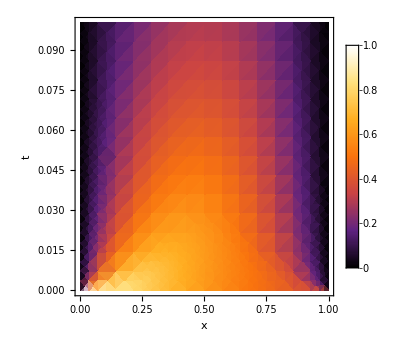

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

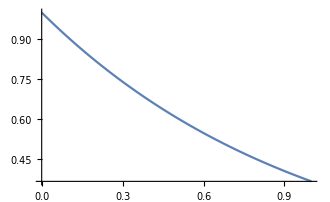

```mathematica
Plot[Exp[-x],{x,0,1}]
```

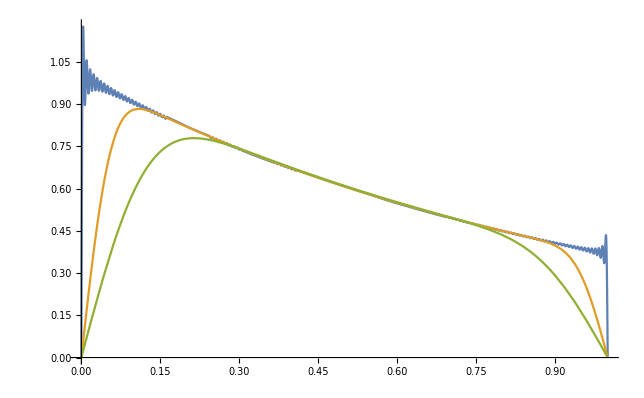

```mathematica
Quiet@Plot[Evaluate@Table[sol,{t,{0,0.001,0.005}}],{x,0,1}]
```

#### Exemplo do Gabriel

```mathematica
bn=FullSimplify[2 Integrate[1/x  Sin[n π x],{x,0,1}],n∈Integers]
```

2 SinIntegral[n π]

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

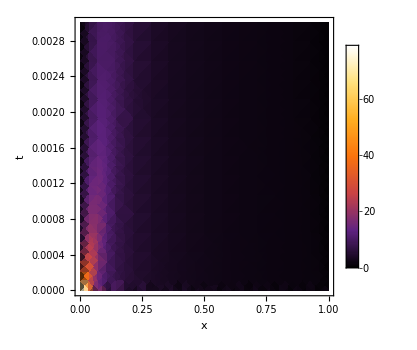

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.003},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

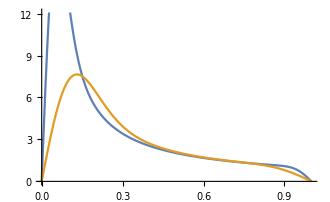

```mathematica
Quiet@Plot[Evaluate@Table[sol,{t,{0.001,0.005}}],{x,0,1}]
```

```mathematica
Integrate[α^2*Exp[-b *x^2],{x,-∞,∞}]
```

ConditionalExpression[(√π α^2)/(√b),Re[b]>0]

## Produces animated GIFs for the solution of the 1D wave equation. Assumes L = c = 1.

```mathematica
SetDirectory[NotebookDirectory[]];
anCoefs[f_,nmax_:100]:=Table[2 NIntegrate[f[x] Sin[n π x],{x,0,1}],{n,1,nmax}]
bnCoefs[g_,nmax_:100]:=Table[2/(n π) NIntegrate[g[x] Sin[n π x],{x,0,1}],{n,1,nmax}]
```

#### Example

```mathematica
f[x_]:= x(x^3-2 x^2+1);
g[x_]:= x(1-x);
an = anCoefs[f,100]//Quiet;
bn = bnCoefs[g,100]//Quiet;

(* I use this function "Compile" to make the evaluation of u faster *)
u = Compile[{{x,_Real},{t,_Real}},Total@Table[(an⟦n⟧ Cos[n π t] + bn⟦n⟧ Sin[n π t])Sin[n π x],{n,1,Length[an]}]
];
```

```mathematica
Animate[Plot[u[x,t],{x,0,1},
PlotRange->{-0.35,0.35}
],{t,0,3}, 
AnimationRate->0.3,
AnimationRepetitions->1,AnimationRunning->False]
```

Animate can be very heavy. I recommend you use it just for basic tests and then, to get better plots, export the outcomes as a GIF.

#### How to export as a GIF

The best way to export as a GIF is to create a list of plots and then export that list.

```mathematica
plots = Table[Plot[u[x,t],{x,0,1},
PlotRange->{-0.35,0.35},
FrameLabel->{"x","u"}
],{t,linspace[0,3,30]}];
```

Table::iterb: Iterator {t,linspace[0,3,30]} does not have appropriate bounds.

```mathematica
Export["PDEs_wave1d_example.gif",plots,ImageResolution->150];
```

### Example gallery

#### Plucked string

```mathematica
a = 0.7;
f[x_]:= Piecewise[{{x/a,0≤x≤a},{(1-x)/(1-a),a≤x≤1}}];
g[x_]:= 0;
an = anCoefs[f,100]//Quiet;
bn = bnCoefs[g,100]//Quiet;
u = Compile[{{x,_Real},{t,_Real}},Total@Table[(an⟦n⟧ Cos[n π t] + bn⟦n⟧ Sin[n π t])Sin[n π x],{n,1,Length[an]}]
];
```

```mathematica
plots = Table[Plot[u[x,t],{x,0,1},
PlotRange->{-1,1},
FrameLabel->{"x","u"}
],{t,N@Subdivide[0,3,10]}];
Export["PDEs_wave1d_plucked.gif",plots];
```

```mathematica
a = 0.7;
f[x_]:= Piecewise[{{x/a,0≤x≤a},{(1-x)/(1-a),a≤x≤1}}];
F = Interpolation[Table[{x,f[x]},{x,0,1,0.1}],InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

#### Gaussian wave-packet

```mathematica
x0 = 0.5;
σ = 0.02;
f[x_]:= Exp[-(x-x0)^2/(2 σ^2)]
g[x_]:= 0;
an = anCoefs[f,100]//Quiet;
bn = bnCoefs[g,100]//Quiet;
u = Compile[{{x,_Real},{t,_Real}},Total@Table[(an⟦n⟧ Cos[n π t] + bn⟦n⟧ Sin[n π t])Sin[n π x],{n,1,Length[an]}]
];
```

```mathematica
plots = Table[Plot[u[x,t],{x,0,1},
PlotRange->{-1,1},
FrameLabel->{"x","u"}
],{t,N@Subdivide[0,3,50]}];
Export["PDEs_wave1d_gaussian.gif",plots];
```

### URLs para acessar esse notebook

https://www.wolframcloud.com/obj/gtlandi/Published/WaveEquation_Annimated_GIFs.nb

Embedding: 
<iframe src=”https://www.wolframcloud.com/obj/gtlandi/Published/WaveEquation_Annimated_GIFs.nb?_embed=iframe” width=”600” height=”800”></iframe>

# Using Fourier Transforms for image compression

This code is based on:
https://demonstrations.wolfram.com/ImageCompressionViaTheFourierTransform/#popup1
by Chris Maes (March 2011)

### The idea

#### 1. Extracting image data

Here is an image:

```mathematica
img = ExampleData[{"TestImage","Lena"}]
```

-Graphics-

A colored image is described essentially by 3 matrices, denoting the intensity of Red, Green & Blue of each pixel (given as numbers between 0 and 1).

```mathematica
imgdata=ImageData[img]
```

{{{0.886275,0.537255,0.490196},{0.886275,0.537255,0.490196},{0.87451,0.537255,0.521569},{0.87451,0.533333,0.501961},504,{0.917647,0.584314,0.482353},{0.901961,0.580392,0.478431},{0.866667,0.509804,0.431373},{0.784314,0.388235,0.352941}},510,{1}}
 |  |  |  |

```mathematica
Dimensions[imgdata]
```

{512,512,3}

This means that the image is 512x512.

For simplicity we are going to make the images black and white, although the basic method also works perfectly fine for colors. 
To make it BW, we essentially take the average over the three colors.

```mathematica
imgBW = N@Map[1-Mean[#]&,imgdata,{2}]
```

{{0.362092,0.362092,0.355556,0.363399,0.36732,0.384314,0.360784,0.366013,0.354248,0.372549,0.360784,0.372549,0.397386,0.36732,0.375163,0.393464,0.394771,0.392157,0.371242,0.379085,0.4,0.398693,0.405229,0.393464,0.4,0.389542,0.397386,0.414379,457,0.470588,0.505882,0.487582,0.496732,0.511111,0.481046,0.498039,0.503268,0.482353,0.51634,0.503268,0.529412,0.512418,0.529412,0.512418,0.522876,0.529412,0.505882,0.499346,0.448366,0.354248,0.343791,0.341176,0.338562,0.346405,0.397386,0.491503},511}
 |  |  |  |

```mathematica
Dimensions[imgBW]
```

{512,512}

This is now just a single 512x512 matrix.

#### 2. Viewing the image data as a sequence

Let us look at one line of the image

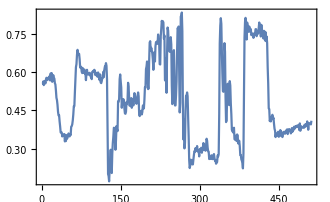

```mathematica
line = imgBW⟦200⟧;
ListLinePlot[line]
```

The color intensities varies along the image in a very irregular fashion. 
Just by looking at this plot does not reveal much about the image. 
For our brain to understand this, we need all lines of the matrix:

```mathematica
ArrayPlot[imgBW]
```

-Graphics-

#### 3. Spectral analysis of the image (Fourier Transform)

But, continuing to think about the single-line, we can now do a spectral analysis and see which frequencies occur more often.

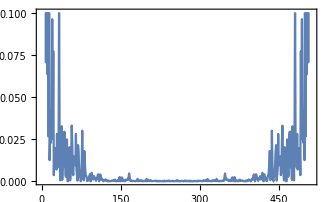

```mathematica
fftline = Fourier[line];
ListLinePlot[Abs[fftline]^2,PlotRange->{0,0.1}]
```

As can be seen, there is a lot of low frequency contributions, then a gap and then a lot of high frequencies: 

- Low frequencies mean features of the image which change slowly. 
- High frequencies mean features which change quickly. 

Now here comes the key idea: 
Our eye is not good at distinguishing rapidly changing features. Low frequency contributions matter much more to us.

This suggests that we can compress the image by:
- Go to Fourier space. 
- Chop off high frequency contributions. 
- Return to real space.

This chops (turns into 0) all elements of fftline which are smaller than 0.1

```mathematica
fftChop = Chop[fftline,10^-1]
```

{11.1931,-0.165897+0.270273 ⅈ,-0.260028-0.561209 ⅈ,-0.859701+1.22006 ⅈ,0.469539-0.283874 ⅈ,0.596803+0.19591 ⅈ,0.72841-0.359341 ⅈ,-0.258504,-0.390938+0.587257 ⅈ,0.277981+0.261022 ⅈ,0.213913+0.132811 ⅈ,-0.564758+0.179016 ⅈ,0.+0.157569 ⅈ,0.-0.449456 ⅈ,0,0.+0.162184 ⅈ,0.+0.134044 ⅈ,0.189987,0.14444,-0.301696,-0.122191+0.100528 ⅈ,0.264689,0,0.+0.138225 ⅈ,0,0.-0.116129 ⅈ,0.+0.138436 ⅈ,0,0.+0.146523 ⅈ,0,0.136508,0,0.+0.32488 ⅈ,0.-0.164959 ⅈ,0,0.+0.14012 ⅈ,0,0.-0.180386 ⅈ,0,0.+0.10393 ⅈ,0,0,0.-0.165941 ⅈ,0.+0.158382 ⅈ,0,0,0,0.+0.127712 ⅈ,0,0,0,-0.118196,0.+0.111531 ⅈ,0,0,-0.114849,0.168189,-0.119215,0,0,0,-0.103516,0.1083,0,0.+0.166421 ⅈ,0,0,0,0.+0.125069 ⅈ,0.-0.12221 ⅈ,0,0,0,0,0,0.-0.101106 ⅈ,0.+0.169956 ⅈ,0,0,0,0.+0.101811 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.-0.101811 ⅈ,0,0,0,0.-0.169956 ⅈ,0.+0.101106 ⅈ,0,0,0,0,0,0.+0.12221 ⅈ,0.-0.125069 ⅈ,0,0,0,0.-0.166421 ⅈ,0,0.1083,-0.103516,0,0,0,-0.119215,0.168189,-0.114849,0,0,0.-0.111531 ⅈ,-0.118196,0,0,0,0.-0.127712 ⅈ,0,0,0,0.-0.158382 ⅈ,0.+0.165941 ⅈ,0,0,0.-0.10393 ⅈ,0,0.+0.180386 ⅈ,0,0.-0.14012 ⅈ,0,0.+0.164959 ⅈ,0.-0.32488 ⅈ,0,0.136508,0,0.-0.146523 ⅈ,0,0.-0.138436 ⅈ,0.+0.116129 ⅈ,0,0.-0.138225 ⅈ,0,0.264689,-0.122191-0.100528 ⅈ,-0.301696,0.14444,0.189987,0.-0.134044 ⅈ,0.-0.162184 ⅈ,0,0.+0.449456 ⅈ,0.-0.157569 ⅈ,-0.564758-0.179016 ⅈ,0.213913-0.132811 ⅈ,0.277981-0.261022 ⅈ,-0.390938-0.587257 ⅈ,-0.258504,0.72841+0.359341 ⅈ,0.596803-0.19591 ⅈ,0.469539+0.283874 ⅈ,-0.859701-1.22006 ⅈ,-0.260028+0.561209 ⅈ,-0.165897-0.270273 ⅈ}

```mathematica
{Length[fftChop],Count[fftChop,0]}
```

{512,419}

Out of the 512 elements of the line, 419 are now zero!
Zero elements do not need to be stored in memory. 
“SparseArray” methods only store the elements which are not zero. 
We have therefore compressed our image!

```mathematica
{ByteCount[SparseArray[fftline]],ByteCount[SparseArray[fftChop]]}
```

{13016,6376}

The number of bytes is reduced by half.

The data is stored in Fourier space. 
When we want to visualize the image, we do an inverse FFT to go back to real space.

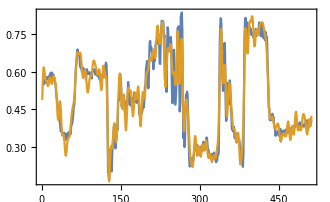

```mathematica
lineChop = InverseFourier[fftChop];
ListLinePlot[{line,lineChop}]
```

As can be seen, the reconstructed data is very similar to the original curve, even though we are only using 1/2 the data.

#### 4. Same thing, but now in 2D

Everything we did above for a single line also applies to the entire image.
It is just not that easy to visualize.

```mathematica
fft = Fourier[imgBW];
ArrayPlot[Abs[fft]^(1/12)]
```

-Graphics-

```mathematica
fftC = Chop[fft,10^-1];
{Times@@Dimensions[fft],Times@@Dimensions[fft]-Count[fftC,0,{2}]}
```

{262144,13428}

The original FT has 262144 nonzero elements. After chopping, we are only left with 13428! 
Or, in terms of kb

```mathematica
IntegerPart[{10^-3. ByteCount[SparseArray[fft]],10^-3. ByteCount[SparseArray[fftC]]}]
```

{6296,786}

The image size is reduced from 6MB to 700kb.

To see if our compression was any good, we compare the original image with the Chopped FT

```mathematica
if = InverseFourier[fftC];
{ArrayPlot[imgBW],ArrayPlot[if]}
```

{-Graphics-,-Graphics-}

Here is the error:

```mathematica
ArrayPlot[Abs[imgBW - if]]
```

-Graphics-

The error is larger in regions with a larger density of details. 
Image compression smears these regions, making the image less crisp.

### Function implementation

```mathematica
ImageBW[img_]:=N@Map[255-Mean[#]&,255 ImageData[img],{2}]

CompressImage[IMG_,imsize_:300]:=Manipulate[
Module[{cf,if},
cf = Chop[fimg,10^Chop[c]];
if = InverseFourier[cf];
Grid[{{
Text@Row[{Style["original (","Label"],IntegerPart[Times@@Dimensions[IMGBW]/10^3.]," kb)"}],Text@Row[{
Style["compressed (","Label"],
IntegerPart[((Times@@Dimensions[IMGBW])-Count[cf,0,{2}])/10^3.],
" kb; ",
IntegerPart[100.((Times@@Dimensions[IMGBW])-Count[cf,0,{2}])/(Times@@Dimensions[IMGBW])],
"% of original size)"

}]
},
{plot,ArrayPlot[if,ImageSize->imsize,PlotRangePadding->None,Frame->False]},
{Text@Style["error","Label"],Text@Style["Power spectrum","Label"]},
{ArrayPlot[Abs[IMGBW - if],ImageSize->imsize,PlotRangePadding->None,Frame->False],ArrayPlot[RotateRight[Sqrt[Sqrt[Abs[cf]]],{128,128}],ImageSize->imsize,PlotRangePadding->None,Frame->False]}}]
],
{{c,1,"compression"},-3,3,.1},Initialization:>{
IMGBW = ImageBW[IMG];
plot :=ArrayPlot[IMGBW,ImageSize->imsize,PlotRangePadding->None,Frame->False];
fimg:=Fourier[N[IMGBW]];
},SynchronousInitialization->False]
```

The function “CompressImage[img]” creates a Manipulate object that allows you to play with different compression ratios.
The function also has the image size as an optional argument: CompressImage[img, imgsize].

### Example gallery (include your own fun pics!)

Tip: don’t leave too many “Manipulate” objects open at the same time. 
It makes the notebook very heavy.

#### Example 1

```mathematica
img=ExampleData[{"TestImage","Lena"}]
```

-Graphics-

```mathematica
(* Click me! *)
CompressImage[img]
```

#### Example 2

```mathematica
CompressImage[-Graphics-]
```

#### Example 3

```mathematica
CompressImage[-Graphics-,500]
```

## Polinomios de langrange

```mathematica
G  = 1/(√(1-2 x λ +λ^2));
SeriesCoefficient[G,{λ,0,2}]
```

1/2 (-1+3 x^2)

```mathematica
LegendreP[2,x]
```

1/2 (-1+3 x^2)

```mathematica
Series[G,{λ,0,4}]
```

1+x λ+1/2 (-1+3 x^2) λ^2+1/2 (-3 x+5 x^3) λ^3+1/8 (3-30 x^2+35 x^4) λ^4+O[λ]^5

```mathematica
Table[LegendreP[n,x],{n,0,4}]
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}

## Visualizing the spherical harmonics

Just run the code below and play with the possible values of l and m.

```mathematica
Clear[l,m,θ,ϕ]
Manipulate[
spheri = SphericalHarmonicY[l,m,θ,ϕ];
ParametricPlot3D[
Evaluate[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}Abs[spheri]],{θ,0,Pi},
{ϕ,-Pi,Pi},PlotRange->{{-.5,.5},{-.5,.5},{-1.1,1.1}},
Mesh->False,
PlotPoints->{36,18},
MaxRecursion->ControlActive[0,2],
ViewAngle->.246,
ImageSize ->{500,377},
Axes->False,
SphericalRegion->True,Boxed->False,
ColorFunctionScaling->False,
ColorFunction->Function[{x,y,z,θ,ϕ},
Evaluate@If[Re@spheri>0,orange,blue]],
PlotLabel->Style[With[{l=l,m=Round@m},TraditionalForm[HoldForm[r==SphericalHarmonicY[l,m,θ,ϕ]]]],14]],
{{l,2,"degree l"},0,7,1,ControlType->Setter},
{{m,0,"order m"},-l,l,1,Appearance->"Labeled"}]
```